# Discrete Phase Space, Computed

### Finite-dimensional quantum mechanics as a computational laboratory in Wolfram Language + QuantumFramework

A qubit, a qutrit, or any d-level system has a phase space just as surely as a particle on a line does, except that the plane (q,p) is replaced by a finite d×d grid of points and the Wigner function becomes a finite table of real numbers, some of them negative. This document is a computation-first tour of that formalism. Every object we discuss, the phase-point operators, the discrete Wigner function, its negativity, the magic monotone mana, the symmetric informationally complete measurements, the mutually unbiased bases, the Weyl transform, and finally the dynamics, is built explicitly and evaluated, so it can be tested, modified, and extended. The conviction behind this style is simple: if we cannot compute it, we do not yet understand it.

We start from the finite Heisenberg-Weyl group (the discrete cousins of position and momentum), build the phase-point operators from it, and use them to define the Wigner function. We then read three physical facts straight off that function: which states are "classical" (the discrete Hudson theorem), how much magic a state carries (mana), and why negativity is the same thing as contextuality. We change frames to the SIC and MIC measurements that underlie the QBist reconstruction of the Born rule, pass through mutually unbiased bases, invert the Wigner map with the Weyl transform, and close by evolving a state directly on the phase-space grid, as a flow generated by the Braasch-Wootters rate matrix, and checking it against ordinary Schrödinger evolution to machine precision. The point of the exercise is that a formalism usually presented on paper becomes something you run.

A note on the environment. Load the paclet once; the phase-space transforms are an experimental part of the framework, so we load the working tree explicitly. Every cell below is meant to be evaluated in order, and you are encouraged to change the dimension d, the state, or the Hamiltonian and watch the numbers move.

```mathematica
PacletDirectoryLoad["/Users/mohammadb/Documents/GitHub/QuantumFramework/QuantumFramework"];
Needs["Wolfram`QuantumFramework`"]
```

## 1. The finite Heisenberg-Weyl group

Continuous phase space is generated by two operators, position and momentum, that fail to commute. The finite-dimensional analogue replaces them by two unitary operators on a d-dimensional space: the shift X, which advances the computational basis Xn=n+1modd, and the clock Z, which stamps each basis state with a phase Zn=ω^n n, where ω=e^(2πi/d). Together they generate the Heisenberg-Weyl (generalized Pauli) group, and the single relation that defines the whole structure is the discrete Weyl commutation law ZX=ω XZ.

Define the clock and shift in dimension d=3 and verify the Weyl relation:

```mathematica
d = 3;
ω = Exp[2 Pi I/d];
X = SparseArray[Table[{Mod[n + 1, d] + 1, n + 1} -> 1, {n, 0, d - 1}], {d, d}];
Z = DiagonalMatrix[Table[ω^n, {n, 0, d - 1}]];
Simplify[Z . X == ω X . Z]
```

True

The result is True: this one identity is the discrete shadow of the Weyl (exponentiated) form of [q̂,p̂]=iℏ, since a finite group has no unbounded commutator to carry the iℏ directly.

A point of the phase-space grid is labelled by a pair (a,b) of integers mod d, and the displacement operator that translates to that point is a phase times a product of powers of shift and clock, D(a,b)∝X^b Z^a. These are the finite translations of phase space; applied to a state they move it rigidly around the grid.

Define the displacement operators and confirm they are unitary:

```mathematica
disp[a_, b_] := (-Exp[I Pi/d])^(a b) MatrixPower[X, b] . MatrixPower[Z, a];
Chop @ Table[UnitaryMatrixQ[disp[a, b]], {a, 0, d - 1}, {b, 0, d - 1}] // Flatten // Union
```

{True}

Every entry is True.

What earns these d^2 operators the name group is closure: the product of any two displacements is again a displacement, up to a phase, D(a,b) D(a',b')=(phase) D(a+a', b+b') with the labels added mod d. Verify that composition law for every pair, and that the leftover phase always has modulus 1:

```mathematica
closureQ[{a1_, b1_}, {a2_, b2_}] := With[
   {m = disp[a1, b1] . disp[a2, b2] . ConjugateTranspose[disp[Mod[a1 + a2, d], Mod[b1 + b2, d]]]},
   With[{ph = m[[1, 1]]}, Simplify[m == ph IdentityMatrix[d] && Abs[ph] == 1]]];
AllTrue[Tuples[Tuples[Range[0, d - 1], 2], 2], Apply[closureQ]]
```

True

The result is True: every product of two displacements collapses to a single displacement times a unit-modulus phase (we divide the product by the expected D(a+a',b+b') and check the quotient is a phase times the identity). That closure, together with the identity D(0,0) and the inverses D(a,b)^†, is exactly the Heisenberg-Weyl group structure; the leftover phases form the group's center. The d^2 displacements are the group we will expand everything in.

The phase τ=-e^(iπ/d) is Gross's odd-d convention: a d-th root of unity (τ^d=1) that makes each D(a,b) have order d and, below, the phase-point operators Hermitian. It is exactly this phase that has no clean counterpart for even d, the deeper reason a covariant qubit Wigner function does not exist. (QuantumFramework stores the conjugate clock Z↦Z^† internally, an ω↔ω^-1 relabeling that leaves the phase-point operators and W unchanged, which is why the hand-built and packaged Wigner values agree throughout.)

We built the clock, shift, and displacements by hand to see the structure in the open, but QuantumFramework already carries them as named operators, and from here on we let it. The generalized Pauli operators are QuantumOperator["X"[d]] and QuantumOperator["Z"[d]]. Confirm that the framework's shift is the very matrix we built, and watch it translate a basis state 0→1:

```mathematica
{Normal[QuantumOperator["X"[3]]["Matrix"]] === Normal[X],
 Normal[QuantumOperator["X"[3]][QuantumState[{1, 0, 0}, 3]]["StateVector"]]}
```

{True,{0,1,0}}

The pair is {True, {0, 1, 0}}: the framework's "X"[3] is our shift matrix exactly, and applied to 0 it returns 1, the finite translation in action. The clock and the Weyl relation come along too, in the conjugate convention noted above. Check that the framework's operators satisfy ZX=ω^-1 XZ:

```mathematica
qX = QuantumOperator["X"[3]]["Matrix"]; qZ = QuantumOperator["Z"[3]]["Matrix"];
Simplify[qZ . qX == ω^-1 qX . qZ]
```

True

True: the framework's "Z"[3] is the clock with ω→ω^-1, so its Weyl relation is the mirror of the one we checked by hand. Same group, same physics, one relabeling of the phase. With these operators in hand, native or hand-built, we can assemble the phase-point operators and the Wigner function.

## 2. Phase-point operators and the discrete Wigner function

In continuous phase space the Wigner function is the expectation of a displaced parity operator. The finite-dimensional construction, due to Wootters and sharpened by Gross for odd prime dimension, mirrors it exactly: to each grid point (q,p) one assigns a phase-point operator A(q,p), a Hermitian unitary built from a displaced discrete parity, and the Wigner function of a state ρ is

W_ρ(q,p)=1/d Tr[ρ A(q,p)].

The d^2 operators A(q,p) form an orthogonal Hermitian basis of operator space, so this is an invertible change of description, not a lossy projection.

Concretely, the parity operator is the mean of all d^2 displacements, and the phase-point operator at (q,p) is that parity displaced there:

\Pi=1/d∑_(a,b) D(a,b),    A(q,p)=D(q,p) \Pi D(q,p)^†,    W_ρ(q,p)=1/d Tr[ρ A(q,p)].

Build \Pi and A from the displacements of Section 1, and confirm \Pi is a genuine parity, Hermitian and squaring to the identity (it reflects the grid about the origin):

```mathematica
Π = (1/d) Sum[disp[a, b], {a, 0, d - 1}, {b, 0, d - 1}];
A[q_, p_] := disp[q, p] . Π . ConjugateTranspose[disp[q, p]];
{Simplify[Π == ConjugateTranspose[Π]], Simplify[Π . Π == IdentityMatrix[d]]}
```

{True,True}

Both True: \Pi is the discrete parity, and each A(q,p) is its translate to the grid point (q,p), the Hermitian unitary the formula promised.

QuantumFramework packages the whole construction. The transform sends a state into the phase-space picture, and the "QuasiProbability" property returns the d×d table W_ρ(q,p). Compute the discrete Wigner function of the computational state 0 in d=3:

```mathematica
ψ0 = QuantumState[{1, 0, 0}, 3];
w0 = ψ0["QuasiProbability"];
MatrixForm @ Chop @ w0
```

(1/3 | 0 | 0
1/3 | 0 | 0
1/3 | 0 | 0)

The output is a real 3×3 table. Two defining properties make it a genuine phase-space distribution. First it is normalized, ∑_(q,p) W=1. Second its marginals are the measurement probabilities: summing W along one axis returns the outcome distribution in the corresponding basis.

Verify normalization and that the position marginal reproduces the Born probabilities:

```mathematica
{Total[w0, 2], Chop @ Total[w0]} == {1, ψ0["ProbabilitiesList"]}
```

True

True. The Wigner function carries the same information as the state, arranged on the grid so that measurements are marginals, exactly as in the continuous theory.

The packaged "QuasiProbability" is nothing other than our trace formula. Evaluate 1/d Tr[ρ A(q,p)] by hand on the phase-point operators we built, and compare:

```mathematica
Whand = Table[(1/d) Tr[ψ0["DensityMatrix"] . A[q, p]], {q, 0, d - 1}, {p, 0, d - 1}];
Simplify[Whand == Normal[w0]]
```

True

True: the framework computes exactly W_ρ(q,p)=1/d Tr[ρ A(q,p)] on the Gross phase-point operators. From here we let it, and read the physics off the table.

## 3. Negativity and the discrete Hudson theorem

Here the finite theory earns its keep. A classical probability distribution on phase space is nonnegative; a Wigner function need not be. For continuous systems Hudson's theorem says the only pure states with a nonnegative Wigner function are Gaussians. Gross proved the finite-dimensional analogue for odd dimension: the pure states with a nonnegative discrete Wigner function are exactly the stabilizer states. Negativity is therefore a sharp, computable signature of non-stabilizer resources, the states that a Clifford computer cannot reach.

Compare a stabilizer state to a non-stabilizer one. The state + (the equal superposition, a stabilizer state in d=3) should be nonnegative; the "strange state" S∝1-2, a standard magic state for the qutrit, should go negative.

Compute the minimum Wigner value for each:

```mathematica
plus = QuantumState[{1, 1, 1}/Sqrt[3], 3];
strange = QuantumState[{0, 1, -1}/Sqrt[2], 3];
{Min @ Chop @ plus["QuasiProbability"], Min @ Chop @ strange["QuasiProbability"]}
```

{0,-1/3}

The first minimum is 0 (the stabilizer state stays nonnegative) and the second is -1/3 (the magic state dips below zero). Negativity is present precisely when the state is outside the stabilizer polytope.

Seeing it helps. Plot the strange state's Wigner table as a heat map over the phase-space grid, diverging from white at zero, blue below, red above, with a legend for the value:

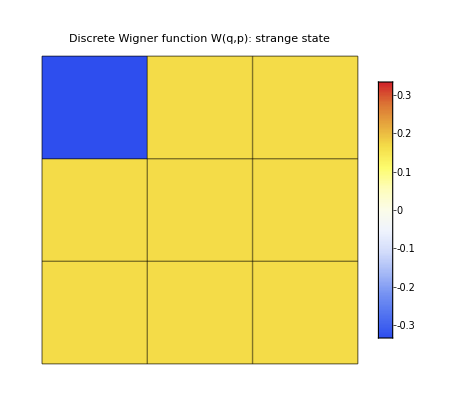

```mathematica
With[{w = N @ strange["QuasiProbability"], m = 1/3.},
 ArrayPlot[w,
  ColorFunction -> (ColorData["TemperatureMap"][(# + m)/(2 m)] &), ColorFunctionScaling -> False,
  Mesh -> True, FrameTicks -> {{{1, "0"}, {2, "1"}, {3, "2"}}, {{1, "0"}, {2, "1"}, {3, "2"}}},
  FrameLabel -> {"position q", "momentum p"},
  PlotLabel -> "Discrete Wigner function W(q,p): strange state",
  PlotLegends -> BarLegend[{(ColorData["TemperatureMap"][(# + m)/(2 m)] &), {-m, m}}]]]
```

The single blue cell is the lone negative entry, W=-1/3; the other eight are the positive 1/6. That one blue square is where the state's nonclassicality, its magic, and its contextuality all live, and every later section is, in one way or another, a way of measuring it.

One subtlety deserves a flag rather than a footnote. Gross's clean theorem is a statement about odd dimension. For even d, and in particular for a qubit, no covariant d×d Wigner function exists, and the standard fix (the one QuantumFramework uses) is a Wootters doubling to a 2d×2d grid. On that grid even the computational qubit state carries negative entries, so the "nonnegative equals stabilizer" reading is an odd-dimensional statement and should not be transported naively to qubits.

Make the failure concrete. Ask the framework for the discrete Wigner function of the qubit 0, itself a stabilizer state, and read off the grid size and the most negative entry:

```mathematica
qubit0 = QuantumState[{1, 0}, 2];
{Dimensions[qubit0["QuasiProbability"]], Min @ Chop @ qubit0["QuasiProbability"]}
```

{{4,4},-1/4}

The table is 4×4, the 2d×2d doubling rather than a 2×2 grid, and its minimum is -1/4: a stabilizer state with a negative Wigner entry. Contrast the qutrit 0 above, which lives on a clean 3×3 grid with minimum 0. This is exactly why Gross's theorem carries the odd-d hypothesis, and why we run the resource story at d=3, where negativity genuinely singles out non-stabilizer states.

## 4. Mana: turning negativity into a magic monotone

Negativity is a yes-or-no witness; a resource theory wants a number. The natural one is the total amount of negativity, and taking its logarithm gives mana, defined by Veitch, Mousavian, Gottesman, and Emerson as

ℳ(ρ)=log ∑_(q,p) |W_ρ(q,p)|.

Because a nonnegative Wigner function sums in absolute value to 1, mana vanishes on stabilizer states and is strictly positive on states with negativity. For odd-dimensional systems (where it is defined, through the covariant Wigner function) it is a genuine magic monotone: it does not increase under the free stabilizer (Clifford-plus-measurement) operations of the resource theory of magic.

Mana is not a named function in the framework; it is one line built from the quasiprobability table, which is exactly the point of having the table. Define it and evaluate it on the stabilizer and magic states:

```mathematica
mana[qs_] := Log @ Total[Abs @ Flatten @ Chop @ qs["QuasiProbability"]];
{mana[plus], mana[strange]} // Simplify
```

{0,Log[5/3]}

The stabilizer state gives 0 and the strange state gives log (5/3)≈0.511, which is in fact the maximum mana over all single-qutrit states: the strange state is the most magical qutrit pure state by this measure. The same object that flagged nonclassicality in the previous section now measures it.

## 5. Negativity is the cost of classical simulation

The negative entry in Section 3 is not a philosophical curiosity; it is the exponent that controls how hard the state is to simulate on a classical computer. The Gottesman-Knill theorem makes stabilizer circuits efficiently simulable, and Veitch, Ferrie, Gross, and Emerson extended that reach: for odd d, any state and operation with a nonnegative Wigner function is also efficiently simulable, by sampling the Wigner function as if it were an ordinary probability distribution. Pashayan, Wallman, and Bartlett showed what happens past that boundary: the sampling still works, but the number of samples it needs grows with the total negativity, quantitatively as the square of the 1-norm ∑_(q,p) W.

So the resource is negativity, and it has a price tag we can read off. Start with the total negativity, the summed weight of the negative part of W:

```mathematica
sumNeg[qs_] := Total @ Select[Flatten @ Chop @ qs["QuasiProbability"], Negative];
{sumNeg[plus], sumNeg[strange]}
```

{0,-1/3}

The stabilizer state contributes 0 and the strange state -1/3. Turn that into the actual simulation overhead: the relevant quantity is the 1-norm 𝒩=∑_(q,p) W=1+2 sumNeg, and the per-copy sampling cost scales as 𝒩^2:

```mathematica
oneNorm[qs_] := Total[Abs @ Flatten @ Chop @ qs["QuasiProbability"]];
{oneNorm[plus]^2, oneNorm[strange]^2} // Simplify
```

{1,25/9}

The stabilizer state costs a factor 1: it is free, exactly the Gottesman-Knill regime. The strange state costs (5/3)^2=25/9 per copy. That number is precisely e^(2ℳ) with the mana ℳ=log (5/3) of Section 4, so mana is literally the per-unit exponent of classical-simulation hardness: t copies or magic gates multiply the overhead to e^(2tℳ), and that exponential is where a quantum advantage, if there is one, has to live.

Two lines keep the accounting honest. First, in this sampling scheme nonnegative measurements are free, so the cost must sit in the state. Confirm the stabilizer (computational-basis) measurements are nonnegatively represented, minimum Wigner entry 0 over their outcome projectors:

```mathematica
Min @ Chop @ Flatten @ Normal @ Table[QuantumState[UnitVector[3, k], 3]["QuasiProbability"], {k, 3}]
```

0

The minimum is 0: every stabilizer effect is nonnegative on the grid, so all the negativity, and all the cost, live in the state. Second, this same negativity is, by Spekkens' theorem, equivalent to contextuality, the failure of any noncontextual model, which is the frame-independent reason it cannot be gauged away and the sense in which Howard, Wallman, Veitch, and Emerson say contextuality "supplies the magic." The operational content, though, is the number above: negativity is what you pay to simulate.

## 6. Changing frames: SIC-POVMs and the Born rule

The Wigner phase-point operators are one frame for operator space; they are not the only useful one. A symmetric informationally complete measurement (SIC) is a set of d^2 subnormalized rank-one effects E_i=1/d ψ_iψ_i, all pairwise equiangular with ψ_iψ_j^2=1/(d+1) for i≠j, that resolve the identity and so form a minimal informationally complete measurement. SICs are the frame at the center of the QBist reconstruction of quantum mechanics, where the Born rule reappears as a coherence condition relating the probabilities of a SIC to those of any other measurement.

The framework ships the standard SICs as named measurements. Build the qutrit Hesse SIC, the most symmetric of the Weyl-Heisenberg-covariant qutrit SICs (its enlarged symmetry group is tied to the Hesse configuration of inflection points on an elliptic curve), and confirm it resolves the identity, the defining property of a POVM:

```mathematica
hesse = QuantumMeasurementOperator["HesseSICPOVM"[]];
elements = hesse["POVMElements"];
{Length[elements], Chop[N[Total[elements] - IdentityMatrix[3]]] // MatrixForm}
```

{9,(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)}

There are 9=d^2 elements and their sum is the identity. The measurement is informationally complete: the nine outcome probabilities carry the eight independent real parameters of a qutrit density matrix (the ninth constraint is normalization), so the state can be reconstructed from SIC statistics alone.

Applying the SIC to a state gives its outcome distribution directly. There is a pleasing coincidence to exploit: the Hesse SIC's fiducial vector is exactly the strange state 1/(√2)(0,1,-1) from Section 3, so the most magical qutrit state is the fiducial of the most symmetric qutrit SIC. Compute the Hesse-SIC probabilities for the strange state, that is, of the SIC's own fiducial:

```mathematica
Simplify @ hesse[strange]["ProbabilitiesList"]
```

{1/3,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12}

The result is one bright outcome 1/d=1/3 and eight equal dim ones 1/(d(d+1))=1/12, exactly the signature of a SIC measured on its own fiducial. More generally these d^2 numbers are a complete, symmetric fingerprint of any state, the "Bureau of Standards" reference measurement in the QBist account.

Why care about a SIC in particular? Because it is the most efficient single measurement for learning an unknown state. Its d^2 outcomes are the minimum for informational completeness, and its symmetry makes the linear reconstruction optimally robust to noise (Scott). Concretely, the state is a simple linear function of the SIC probabilities,

ρ=d(d+1)∑_i p_i E_i-I,

so the numbers a SIC measurement returns are exactly the coordinates of ρ. Reconstruct the strange state from its own Hesse-SIC statistics:

```mathematica
p = hesse[strange]["ProbabilitiesList"];
Ei = hesse["POVMElements"];
ρrec = d (d + 1) Sum[p[[i]] Ei[[i]], {i, d^2}] - IdentityMatrix[d];
Simplify[ρrec == strange["DensityMatrix"]]
```

True

True: the nine probabilities a single SIC measurement produces are enough to rebuild the entire density matrix, and no smaller measurement could. That is the operational reason SICs matter, they are optimal quantum-state tomography in one device, and it is why they have been realized in the laboratory for exactly that purpose.

## 7. Minimal informationally complete measurements more generally

A SIC is the most symmetric member of a broader family: the minimal informationally complete measurements (MICs), any d^2 operators that resolve the identity and span operator space. DeBrota, Fuchs, and Stacey study these as the natural reference frames for a probabilistic representation of quantum theory, and the discrete Wigner function itself can be recovered from a suitable (Weyl-Heisenberg-covariant) MIC via the DeBrota-Stacey construction. The framework builds several: a MIC from the Gell-Mann basis, random MICs, and the Wigner-MIC that ties this section back to Section 2.

Build the Gell-Mann MIC for the qutrit and confirm it too is a valid informationally complete POVM:

```mathematica
gm = QuantumMeasurementOperator["GellMannMICPOVM"[3]];
els = gm["POVMElements"];
{Length[els], Chop[N[Total[els] - IdentityMatrix[3]]] // MatrixForm}
```

{9,(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)}

Nine elements summing to the identity: a MIC that is informationally complete without being symmetric. The lesson is that "informationally complete" is the load-bearing property and symmetry is a bonus that the SIC adds on top. This is why MICs, not SICs, are what a real laboratory works with: a physical detector is almost never a perfect SIC, but as long as it is informationally complete the same linear inversion ρ=∑_i p_i D_i (now with the dual frame D_i of a generic MIC rather than the tidy SIC formula) reconstructs the state, just with a less favorable error scaling. The SIC is the optimum you design toward; a MIC is the apparatus you actually have.

## 8. Mutually unbiased bases

Where a SIC is a single optimal measurement, mutually unbiased bases are an optimal collection of measurements. Two orthonormal bases are unbiased when a definite state in one is completely uncertain in the other, a_ib_j^2=1/d for all i,j, so that measuring in the wrong basis yields no information. For prime-power d there are d+1 such bases, the maximal set, and they give the most efficient state tomography (the optimality is the Wootters-Fields result; the explicit prime-d construction is Ivanovic's). The framework provides the Ivanovic construction directly.

Build one Ivanovic basis for d=3 and check that it is unbiased with respect to the computational basis:

```mathematica
mub = QuditBasis["Ivanovic"[3, 1]];
Chop @ Abs[mub["Matrix"]]^2 // MatrixForm
```

(1/3 | 1/3 | 1/3
1/3 | 1/3 | 1/3
1/3 | 1/3 | 1/3)

Every entry is 1/3: a state sharp in the computational basis is maximally spread over the Ivanovic basis. These are the finite-dimensional embodiment of complementarity.

The payoff is twofold, and both halves are practical. For tomography, the d+1 mutually unbiased bases are the most efficient set of projective measurements: they read out the d^2-1 parameters of a state with the fewest settings and the smallest statistical error, the basis-measurement counterpart of what a SIC does in one shot. For cryptography, complementarity is the security of quantum key distribution: an eavesdropper who guesses the wrong basis learns nothing, precisely the flat 1/d we just computed, so encoding key bits in mutually unbiased bases (BB84 for the qubit, its qudit generalizations here) makes any interception show up as errors. The 1/3 in that table is not a curiosity; it is the reason MUBs are the workhorse of both quantum tomography and quantum key distribution.

## 9. The Weyl transform: from phase space back to operators

Everything so far has pushed states into a phase-space representation. The inverse map is the Weyl transform, which reconstructs an operator from its phase-space symbol; the Wigner and Weyl transforms are the two directions of the finite Weyl-Wigner correspondence. Because the phase-point operators are a complete orthogonal basis, the round trip is exact: transforming a state to phase space and back returns the original state.

Confirm the round trip on the strange state:

```mathematica
back = QuantumWeylTransform @ QuantumWignerTransform[strange];
FullSimplify[ComplexExpand[Normal[back["DensityMatrix"] - strange["DensityMatrix"]]]] // MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

The difference is the zero matrix. The entries come back as exact cube-root surds inside a sparse array, so we Normal-unpack and ComplexExpand before FullSimplify can cancel them (plain Chop does not reach inside the structured entries). The phase-space picture loses nothing; it is a faithful, invertible re-encoding of the state, which is what licenses us to do physics in it.

That invertibility is the whole license for the phase-space program. The classical-simulation sampling of Section 5 is only valid because the encoding loses nothing, and the dynamics of the next section will run entirely on the grid and return to a density matrix through exactly this transform. The Weyl map is the return ticket that turns phase space from a one-way picture into a working computational tool.

## 10. Dynamics: the transition-rate generator

The deepest payoff is that phase space is not just a static portrait but a place to do dynamics. Braasch and Wootters showed that continuous-time evolution of the discrete Wigner function is governed by a transition-rate generator: writing the Wigner function as a vector W, its evolution obeys Ẇ=R W, where the rate matrix R is obtained by expanding the Hamiltonian in displacement operators, which amounts to taking the phase-space symbol of H and dividing out the unitary i. QuantumFramework computes exactly this generator through HamiltonianTransitionRate.

Build the transition-rate matrix for a Hermitian qutrit Hamiltonian, the nearest-neighbor hopping H=X+X^† on the three-site ring:

```mathematica
Hq = QuantumOperator[X + ConjugateTranspose[X], {1}];
rate = HamiltonianTransitionRate[Hq];
{Dimensions[rate], Chop @ Max @ Abs @ Im @ rate}
```

{{9,9},0}

The generator is a 9×9 matrix acting on the nine-component Wigner vector of the qutrit: the discrete-phase-space analogue of the Liouville operator that pushes a classical distribution around phase space. For this real-symmetric H the generator is real (the second entry is 0), the special case in which its imaginary part vanishes. Reality alone does not make R a classical stochastic generator, though: Braasch and Wootters show that the transition rates, like the Wigner function itself, can be negative, so even this real R need not have the nonnegative off-diagonal rates a genuine phase-space transport process would require. In general R is complex as well.

Now integrate the motion on the grid. The Wigner function is a real nine-vector W, and the generator propagates it by the linear flow W(t)=e^Rt W(0). Evolve 0 to t=1 and check that probability is conserved on the grid:

```mathematica
W0 = Flatten[N[QuantumState[{1, 0, 0}, 3]["QuasiProbability"]]];
Wt = MatrixExp[rate] . W0;
Total[Wt]
```

1.

The total is 1: the flow e^Rt keeps the Wigner vector normalized, as any legitimate phase-space evolution must. Map the evolved vector back to a density matrix with the Weyl transform and compare against direct Schrödinger evolution:

```mathematica
onGrid = QuantumWeylTransform[QuantumState[Wt, QuantumBasis["Wigner"[3]]]];
exact = QuantumState[MatrixExp[-I N[Hq["Matrix"]]] . {1, 0, 0}, 3];
Norm[Normal[onGrid["DensityMatrix"]] - exact["DensityMatrix"]]
```

3.15065×10^-16

The two agree to machine precision (∼10^-16): the dynamics computed as a flow on the discrete Wigner grid is the Schrödinger equation, expressed in phase-space language. One idiom worth flagging: it is the generator R, applied as e^Rt, that drives the grid here; the state-level QuantumEvolve wrapper handed a Wigner-picture state does not yet propagate it, so the generator route above is the one to use.

The construction extends to open systems. Each jump operator gets its own rate matrix through LindbladTransitionRates, and the full open-system generator is the Hamiltonian rate plus the jump rates, G=R_H+∑_k γ_k R_L_k, still acting on the same nine-component Wigner vector. Build that generator for a decaying qutrit, the lowering jump L=01+12 with H=0 and rate 1, and evolve 2 on the grid to t=1:

```mathematica
Lop = QuantumOperator[{{0, 1, 0}, {0, 0, 1}, {0, 0, 0}}, {1}];
Hz = QuantumOperator[ConstantArray[0, {3, 3}], {1}];
G = HamiltonianTransitionRate[Hz] + Total @ LindbladTransitionRates[{Lop}];
Wd = MatrixExp[G] . Flatten[N[QuantumState[{0, 0, 1}, 3]["QuasiProbability"]]];
Total[Wd]
```

1.

The total is again 1: the dissipative flow is trace-preserving on the grid. Map the evolved Wigner vector back and compare against a direct integration of the Lindblad master equation, where the rule-form signature {L}→{γ} pairs each jump operator with its rate (the positional form does not converge here):

```mathematica
openGrid = QuantumWeylTransform[QuantumState[Wd, QuantumBasis["Wigner"[3]]]];
exactOpen = QuantumEvolve[Hz, {Lop} -> {1}, QuantumState[{0, 0, 1}, 3], {t, 0, 1}];
Norm[Normal[openGrid["DensityMatrix"]] - (Normal[exactOpen["DensityMatrix"]] /. t -> 1.)]
```

4.89568×10^-9

The grid-evolved dissipative state matches the directly integrated master equation to solver tolerance (∼10^-9). Closed or open, the phase-space picture carries a genuine generator on the discrete grid: the Braasch-Wootters rate matrix R_H for the unitary part, and LindbladTransitionRates for the dissipative part.

## Where this leaves us

We built the finite phase-space formalism from the ground up and, at every step, computed rather than asserted. In order:

The Heisenberg-Weyl group (clock Z, shift X, displacements D(a,b)) is the finite analogue of position and momentum, defined by the one relation ZX=ωXZ.

The discrete Wigner function W_ρ(q,p)=1/d Tr[ρA(q,p)] is a faithful, invertible re-encoding of a state whose marginals are the measurement probabilities.

Negativity of W is a computable signature that ties several statements together: it marks non-stabilizer states (the discrete Hudson theorem, odd d), it is quantified by mana as an odd-d magic monotone, it sets the cost of classical simulation (the sampling overhead ∼e^(2ℳ), free in the nonnegative Gottesman-Knill regime), and, by Spekkens' equivalence, it is a signature of contextuality.

SIC and MIC measurements are alternative frames for the same operator space, minimal and informationally complete, underlying the QBist reconstruction of the Born rule.

Mutually unbiased bases are the optimal set of complementary measurements, d+1 of them for prime-power d.

The Weyl transform inverts the Wigner map exactly, and the Braasch-Wootters transition-rate generator Ẇ=R W propagates the Wigner vector on the grid: closed evolution as the flow e^Rt reproduces Schrödinger to machine precision, and the open (dissipative) case, with LindbladTransitionRates supplying the jump rates, matches the directly integrated master equation.

What makes this more than a change of notation is that each classical result became an executable check: Hudson's theorem is a comparison of two Min values, mana is a one-line functional of a table, and the Braasch-Wootters generator, applied as e^Rt, reproduces Schrödinger evolution on the grid to machine precision. One boundary is worth remembering: the odd-dimensional machinery is exact and covariant, and it is where the on-grid evolution above runs cleanly; the even-dimensional qubit case rides on the doubled 2d×2d grid, whose read-back is not canonical, and the state-level QuantumEvolve phase-space wrapper does not yet drive the grid (the generator route does). With those caveats, the phase-space picture is a working laboratory for finite-dimensional quantum mechanics, and the same tools scale straight to multi-qudit systems and to the resource theories built on negativity.

## References

W. K. Wootters, "A Wigner-function formulation of finite-state quantum mechanics," Ann. Phys. 176, 1 (1987).

K. S. Gibbons, M. J. Hoffman, W. K. Wootters, "Discrete phase space based on finite fields," arXiv:quant-ph/0401155.

D. Gross, "Hudson's theorem for finite-dimensional quantum systems," arXiv:quant-ph/0602001.

R. W. Spekkens, "Negativity and contextuality are equivalent notions of nonclassicality," arXiv:0710.5549.

V. Veitch, S. A. H. Mousavian, D. Gottesman, J. Emerson, "The resource theory of stabilizer computation," arXiv:1307.7171.

M. Howard, J. Wallman, V. Veitch, J. Emerson, "Contextuality supplies the magic for quantum computation," arXiv:1401.4174.

D. Gottesman, "The Heisenberg representation of quantum computers," arXiv:quant-ph/9807006.

V. Veitch, C. Ferrie, D. Gross, J. Emerson, "Negative quasi-probability as a resource for quantum computation," arXiv:1201.1256.

H. Pashayan, J. J. Wallman, S. D. Bartlett, "Estimating outcome probabilities of quantum circuits using quasiprobabilities," arXiv:1503.07525.

C. Ferrie, J. Emerson, "Frame representations of quantum mechanics and the necessity of negativity in quasi-probability representations," arXiv:0711.2658.

J. B. DeBrota, C. A. Fuchs, B. C. Stacey, "The varieties of minimal tomographically complete measurements," arXiv:1812.08762.

J. B. DeBrota, B. C. Stacey, "Discrete Wigner functions from informationally complete quantum measurements," arXiv:1912.07554.

I. D. Ivanovic, "Geometrical description of quantal state determination," J. Phys. A 14, 3241 (1981); W. K. Wootters, B. D. Fields, "Optimal state-determination by mutually unbiased measurements," Ann. Phys. 191, 363 (1989).

Z. Braasch, W. K. Wootters, "Transition probabilities and transition rates in discrete phase space," arXiv:2007.10187.